# π Project Report

Math 242 — Modern Computational Mathematics
Done by: Dagmawe Haileslassie

## Problem Statement - 1

I will use the following sum formula to compute approximation of π:
	1/π = (2*Sqrt[2]/9801) * SUM[ (4 k)! (1103 + 26390 k)/(k!)^4*396^(4k)]

This formula is known as the Ramanujan formula for π. I will investigate how the number of correct digits in the approximation of π depends on the number of terms used in the sum.

## Implementation - Ramanujan

First, I will use a do loop with a print statement instead of a module to visualize what exactly is going on in my code. This helps me understand the sequence, and point out any problems early.

```mathematica
Do[Print[(((4i)!)*(1103+26390i))/((i!)^4*396^(4i))], {i,0,5}]
```

1103

27493/1024635744

209545/933225251451052032

14047775/7041226539731908913606688768

8493041375/461740313229488003214951761227271897088

9125262601/52568403264521053657025165532135121484783812608

Now let’s put the formula above into a module, to avoid repeatedly entering a number as a range in a normal Do loop.

```mathematica
ramanujan[n_]:=Module[{sum = 0},
Do[sum += (((4i)!)*(1103+26390i))/((i!)^4*396^(4i))
, {i,0,n}];
sum*((2*Sqrt[2])/9801) (*Multiplying the sum with the constant *)
]
```

```mathematica
N[1/ramanujan[1]] (* Let's check to see if it works*)
```

3.14159

Now to calculate the number of correct digits past the decimal point, we will use the correctDigits module written below. This module helps us analyze how accurate the Ramanujan formula really is.

```mathematica
correctDigits1[n_]:=Module[{approx,i=0},
approx= 1/ramanujan[n];
While[ RealDigits[approx,10,1,i]⟦1,1⟧==RealDigits[Pi,10,1,i]⟦1,1⟧,i--];
-i-1 (* the number of correct digits after the decimal point *)
]
```

Now that we can calculate and compare how similar the actual number Pi is to the result of the Ramanujan formula. Let us plot the number of correct digits for various values of n. First we need all the data to create the plot therefore we should start with a table function. When writing a table function we need to specify how many values our variable n will take. I set n to range from 100 up to 1000, with a 100 digit increment.

```mathematica
nDigits=Table[{n,correctDigits1[n]},{n,100,1000,100}]
```

{{100,805},{200,1604},{300,2402},{400,3201},{500,3999},{600,4797},{700,5596},{800,6394},{900,7191},{1000,7990}}

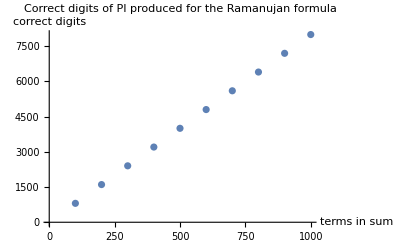

```mathematica
ListPlot[nDigits,AxesLabel->{"terms in sum","correct digits"}, PlotLabel-> "Correct digits of PI produced for the Ramanujan formula"  ]
```

We see the number of digits increases in a linear form which helps us assume that the even if we collected more data there is a significant trend here that can help us make a successful conjuncture.

## Problem Statement - 2

I will use the following sum formula to compute approximation of π:
	1/π = (12) * SUM[ (-1)^k(6k)!(13591409 + 545140134k)/ ((3k)!)(k!)^3(640320)^(3k+3/2)

This formula is known as the Chudnovsky formula for π which was written on 1989. I will investigate how the number of correct digits in the approximation of π depends on the number of terms used in the sum.

## Implementation - Chudnovsky

```mathematica
chudnovsky[n_]:=Module[{sum = 0},
Do[sum += (((-1)^i)*((6*i)!)*(13591409+545140134*i))/(((3*i)!)*((i!)^3)*(640320)^(3*i+3/2))
, {i,0,n}];
sum*(12)
]
```

```mathematica
N[1/chudnovsky[1]]
```

3.14159

The module below helps us analyze how accurate the Chudnovsky formula really is when compared to the decimal PI.

```mathematica
correctDigits2[n_]:=Module[{approx,i=0},
approx= 1/chudnovsky[n];
While[ RealDigits[approx,10,1,i]⟦1,1⟧==RealDigits[Pi,10,1,i]⟦1,1⟧,i--];
-i-1 (* the number of correct digits after the decimal point *)
]
```

Now that we can calculate and compare how similar the decimal PI is to the result of the Chudnovsky formula. Just like we did above, let us plot the number of correct digits for various values of n. First we need to collect data points to create the plot using a table function. As we have seen above when writing a table function we need to specify how many values our variable n will take. I set n to range from 10 up to 100 this time, with a 10 digit increment.

```mathematica
nDigits2=Table[{n,correctDigits2[n]},{n,10,100,10}]
```

{{10,155},{20,296},{30,439},{40,580},{50,722},{60,864},{70,1006},{80,1148},{90,1289},{100,1432}}

One thing to note is that when running the table function on the Chudnovsky formula there was a considerable time difference when compared to the Ramanujan formula.

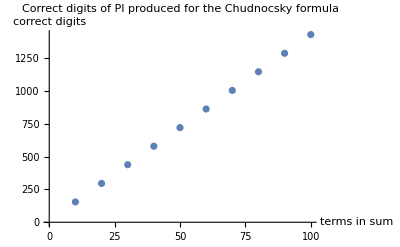

```mathematica
ListPlot[nDigits2,AxesLabel->{"terms in sum","correct digits"},PlotLabel-> "Correct digits of PI produced for the Chudnocsky formula"]
```

We see the number of digits increases in a linear form which helps us assume that even if we collected more data there is a significant trend here that can help us make a successful conjuncture. As the number of terms increases the number of correct digits also linearly increases, by this I mean we can roughly see that the number of digits when provided 20 terms is double the amount to that of 10 terms.

## Problem Statement

I will use the following system of equations to compute approximation of π: 
a[i]=(a[i-1]+b[i-1])/2;
b[i] = Sqrt[(a[i-1]*b[i-1])];
c[i] = a[i]^2-b[i]^2;
s[i] = s[i-1]-(2^i*c[i]);
p[i] = (2 a[i]^2)/s[i]

This formula is written by Salamin and Brent in 1976. Just like the previous formulas I will investigate how the number of correct digits in the approximation of π depends on the number of terms used in the sum.

## Implementation - Salamin and Brent

```mathematica
salaminbrent[n_]:=Module[{a, b, c, s, p},                  (* stating all of the local variables *)
a[0]=1;
b[0] = 1/Sqrt[2];
s[0] = 1/2;
Do[a[i]=(a[i-1]+b[i-1])/2;
b[i] = Sqrt[(a[i-1]*b[i-1])];
c[i] = a[i]^2-b[i]^2;
s[i] = s[i-1]-(2^i*c[i]);
p[i] = (2 a[i]^2)/s[i]
,{i,1,n}];     
p[n]                                                                       (* return p[n] *)
]
```

```mathematica
N[salaminbrent[10]]
```

3.14159

```mathematica
correctDigits3[n_]:=Module[{approx,i=0},
approx=salaminbrent[n];
While[ RealDigits[approx,10,1,i]⟦1,1⟧==RealDigits[Pi,10,1,i]⟦1,1⟧,i--];
-i-1 (* the number of correct digits after the decimal point *)
]
```

```mathematica
nDigits=Table[{n,correctDigits3[n]},{n,1,10,1}]
```

{{1,1},{2,3},{3,9},{4,20},{5,42},{6,85},{7,173},{8,347},{9,697},{10,1393}}

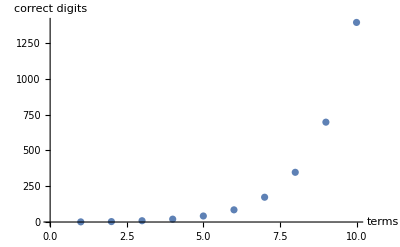

```mathematica
ListPlot[nDigits,AxesLabel->{"terms","correct digits"}]
```

We see the number of digits increases in an exponential form this time. When looking at the graph there was a constant and slight increase in the number of correct digits until n=6 then we can see that the Y axis dramatically increases as we move along the X axis and increase the terms . Unlike the rest of the formulas I am very curious to see the runtime for this specific code.

## Conclusions and Conjunctures

As shown in the plots above, the number of correct digits for the Ramanujan formula as well as the Chudnovsky formula doubles every-time there is an increase in n.  I conjecture that this pattern holds as n increases for both formulas, though I only tested values of n up to 1000 for Ramanujan and a 100 for Chudnovsky. One important detail to note is that the Chudnovsky formula runs slower than the Ramanujan. 
In the third plot, the number of correct digits exponentially increases with an increase to n. It is also important to note that this increase doesn’t happen until n=6.  I conjecture that this pattern holds as n increases for both formulas, though I only tested values of n up to 10 iterations. 
When relating all the formulas to each-other we can see that the Salamin and brent formula is the most accurate one where as the other two formulas are some what of  mirror images to each-other. Therefore the Salamin and brent formula seems to be the most practical way of computing lots of digits of π

## Limitations and Extensions

My method of running all of the formula using a module and a range of [n] is not a great way of figuring out how many terms are required to obtain a desired number of digits of π. I believe that there should perhaps be a way in which I instantly know how many correct digits I would achieve from a specific number or n. Perhaps this could be studied theoretically (rather than computationally) using results about rates of convergence of infinite series.
I would also have liked to calculate the runtime for all of the formulas listed in this notebook. I thought the run time seemed to increase as we go from Ramanujan to Salamin and Brent. It is intuitive that because Salamin and Brent was a recursive formula that there would be a longer run time but the difference bettween the Ramanujan and Chudnovsky formula is something I couldn’t really explain. Which in my opinion can be an extension for future work.